# 2D Tiling

## Used and explained in the article “On the K-theory of C^*-algebras for substitution tilings (a pedestrian version)” by Daniel Gonçalves and Maria Ramirez-Solano.

## 1.Definition of prototiles and substitution of prototiles (user input)

```mathematica
(*prototile = a polygon with a corner at the origin  = list of points in the plane, called locations, which represent the corners of the polygon, listed in counterclockwise order, starting at the origin*)
halfhexCorners={{0,0},{4,0},{3,Sqrt[3]},{1,Sqrt[3]}};
p1=halfhexCorners;
p2=Map[rotation180,p1];
p3=Map[RotationMatrix[π/3].#&,p1];
p4=Map[rotation180,p3];
p5=Map[RotationMatrix[π/3].#&,p3];
p6=Map[rotation180,p5];

prototiles={p1,p2,p3,p4,p5,p6};


(*inflation factor*)
λ=2;

(* tile = (prototilenumber, location) *)
(* tEdge = (tilenumber, edgenumber in the prototile) *)
(* tVertex = (tilenumber, vertexnumber in the prototile)  *)
(* protoEdge = (prototilenumber, edgenumber in the prototile) *)
(* protoVertex = (prototilenumber, vertexnumber in the prototile)  *)
(* wp0 = {(prototilenumber, location),(prototilenumber, location)... } = list of tiles*)
origins1={{2,0},{8,0},{6,2 √3},{2,2 √3}};
origins2=Map[rotation180,origins1];
origins3=Map[RotationMatrix[π/3].#&,origins1];
origins4=Map[rotation180,origins3];
origins5=Map[RotationMatrix[π/3].#&,origins3];
origins6=Map[rotation180,origins5];

wp1=Partition[Riffle[{1,5,2,4},origins1],2];
wp2=Partition[Riffle[{2,6,1,3},origins2],2];
wp3=Partition[Riffle[{3,2,4,6},origins3],2];
wp4=Partition[Riffle[{4,1,3,5},origins4],2];
wp5=Partition[Riffle[{5,4,6,1},origins5],2];
wp6=Partition[Riffle[{6,3,5,2},origins6],2];

wPrototile={wp1,wp2,wp3,wp4,wp5,wp6};


MAXDegreeOfBoundaryVertices=2;(*USUALLY 1*)

(*auxiliary functions for constructing prototiles*)
rotation90=Function[location,{-location⟦2⟧,location⟦1⟧}];
rotation180=Function[location,-location];
rotation270=Function[location,{location⟦2⟧,-location⟦1⟧}];

color=Join[{Red,RGBColor[.92,.26,.47],RGBColor[0,.71,.02],RGBColor[.35,.73,.51],RGBColor[.1,.52,1],RGBColor[.29,.65,1], Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen,Red,Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen},Table[RGBColor[(i/8+.5)/1.5,0,0],{i,1,8}],
Table[RGBColor[0,(i/8+.5)/1.5,0],{i,1,8}],
Table[RGBColor[0,0,(i/4+.5)/1.5],{i,1,4}]]
label={a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z};
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

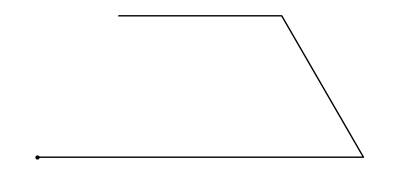
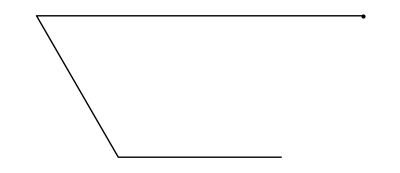
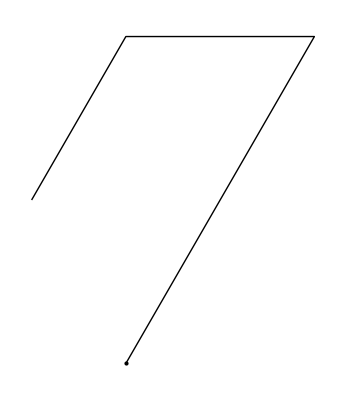
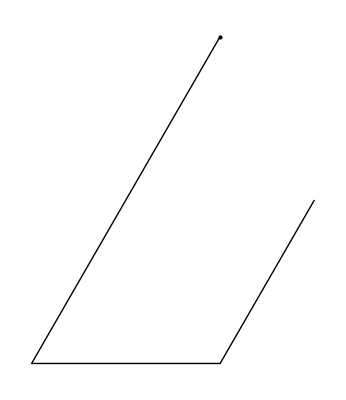
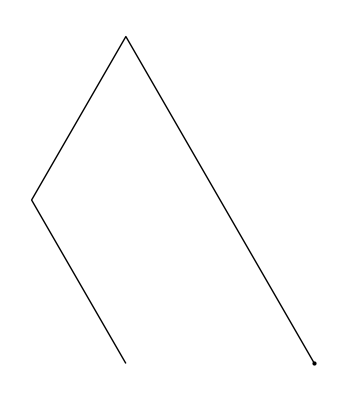
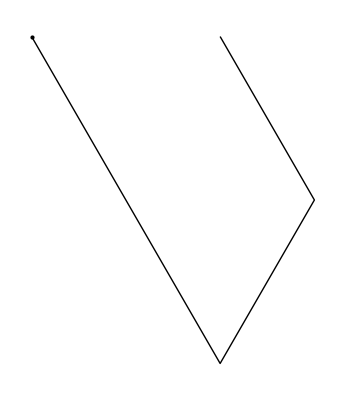

```mathematica
Map[Graphics[{Line[#],Point[#⟦1⟧]}]&,prototiles]
```

Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

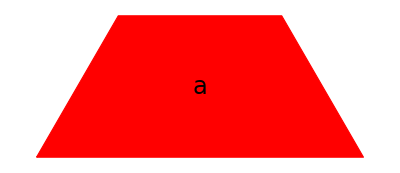
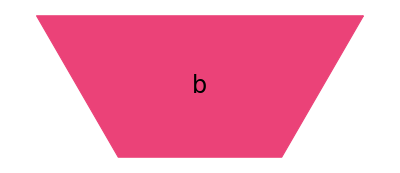
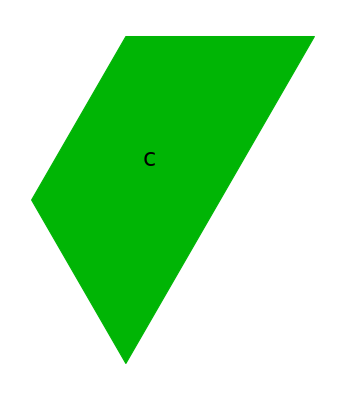
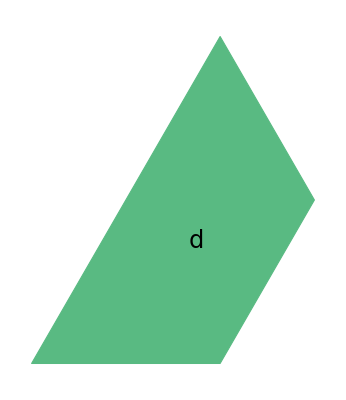
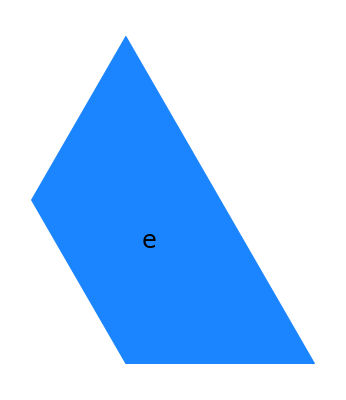
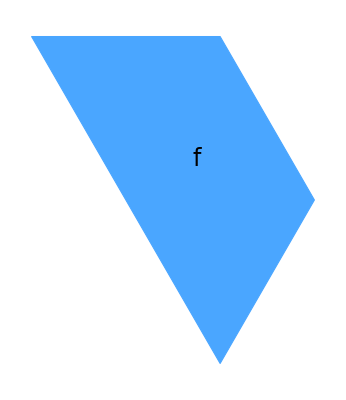

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]
polygonsLabels=Function[{polygonCorners,colorsIndices},Table[{
label⟦colorsIndices⟦i⟧⟧,Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]},
{i,1,Length[polygonCorners]}]];polygonsColorsBoundaries=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]

Table[Graphics[polygonsColorsBoundaries[{prototiles⟦i⟧},{i}]],{i,1,Length[prototiles]}]
```

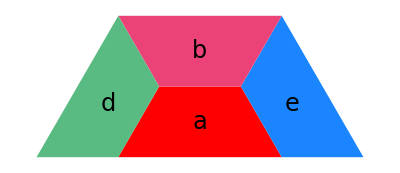
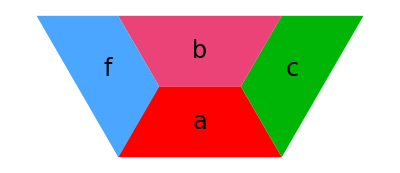
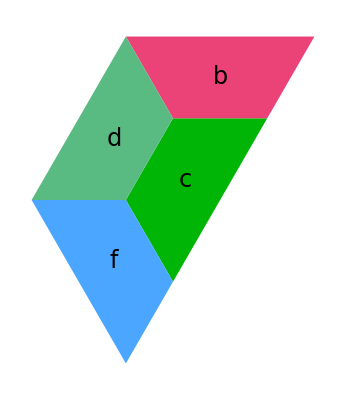
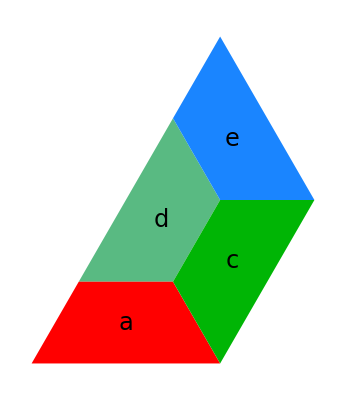
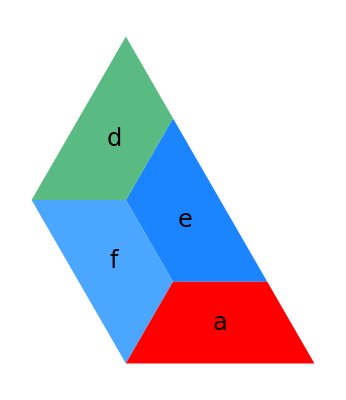
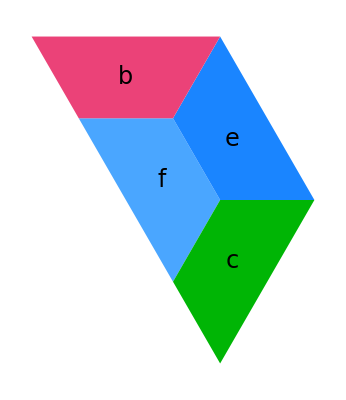

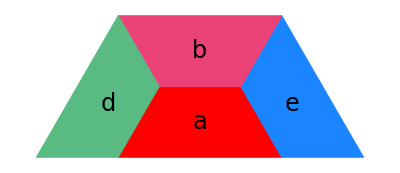
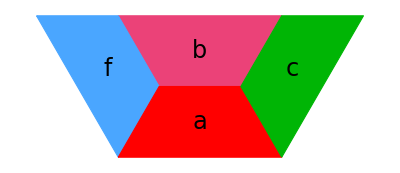

```mathematica
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];

Table[Graphics[polygonsColors[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
Table[Graphics[polygonsColorsBoundaries[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
```

## 2.Defining substitution ω(tiles) (run 1)

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColorsPlain=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]


(*ωTile(tile) = list of tiles which represent the substituted tile  *)
ωTile=Function[tile,Module[{tiles,prototileNumber,translation},
{prototileNumber,translation}=tile;
tiles=wPrototile⟦prototileNumber⟧;
(*tiles +λ translation*)
Table[{tiles⟦i⟧⟦1⟧,tiles⟦i⟧⟦2⟧+ λ translation},{i,1,Length[tiles]}]
]];
(*AddTranslation=Function[{locations,translation},Table[locations⟦i⟧+translation,{i,1,Length[locations]}]];*)
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];
(*ω substitutes a list of tiles by substituting each tile individually *)
ω=Function[tiles,Flatten[Map[ωTile,tiles],1]]
supertile=Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

(*maximum number smaller than the limit*)
bsearchMin[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list⟦m⟧==elem,While[list⟦m⟧==elem,m++];
Return[m-1]];
If[list⟦m⟧<elem,n0=m+1,n1=m-1]];
If[list⟦m⟧<elem,m,m-1]];

(*minimum number larger than the limit*)
bsearchMax[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[list[[m]]==elem,m--];
Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]];


varpepsilonZero=10^(-10);
positiveEdgeQ=Function[edgeLocation,Module[{x,y},{x,y}=edgeLocation⟦2⟧-edgeLocation⟦1⟧;If[x>0 || (Abs[x]<varpepsilonZero&&y>0),True,False]]];
(*computeEdgesDirections= {{1,1,1,-1,-1,,,},{1,1,-1,..}} where 1=samedirection, -1 opposite direction *)
computeEdgesDirections=Function[tileLocations,Module[{edge,lastedge},
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[positiveEdgeQ[edge]==True,1,-1],{i,1,Length[tileLocations]-1}],If[positiveEdgeQ[lastedge]==True,{1},{-1}]]]];
prototilesDirections=Map[computeEdgesDirections,prototiles]
prototilesLengths=Map[Length,prototiles]

Unflatten=Function[{list,lengths},Module[{k},
k=0;
Table[Table[k++;list⟦k⟧,{i,1,lengths⟦j⟧}],{j,1,Length[lengths]}]]];
swapVerticesofEdge=Function[v1v2,{v1v2⟦2⟧,v1v2⟦1⟧}];

cyclicRange=Function[{interval,n},Module[{a,b},
{a,b}=interval;
If[a≤ b,Range[a,b],
Join[Range[a,n],Range[b]]]]];
drawProtoEdge=Function[protoEdge,Module[{loc},
(*protoEdge={prototilenumber,number of edge on prototile} *)
loc=prototiles⟦protoEdge⟦1⟧⟧;
Graphics[{color⟦protoEdge⟦1⟧⟧,Polygon[loc], Black, Line[{loc⟦protoEdge⟦2⟧⟧,loc⟦Mod[protoEdge⟦2⟧+1,Length[loc],1]⟧}]}]]];
drawProtoVertex=Function[protoVertex,Module[{loc},loc=prototiles⟦protoVertex⟦1⟧⟧;Graphics[{color⟦protoVertex⟦1⟧⟧,Polygon[loc],Black,Point[{loc⟦protoVertex⟦2⟧⟧}]}]]];
```

Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[tiles,Flatten[ωTile/@tiles,1]]

Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

{{1,-1,-1,-1},{-1,1,1,1},{1,-1,-1,1},{-1,1,1,-1},{-1,-1,1,1},{1,1,-1,-1}}

{4,4,4,4,4,4}

```mathematica
(*ω(prototiles)*)
prototiles//Length
(*ω(prototiles)*)
prototiles//Length
Table[Graphics[polygonsColors[ComputeLocations[ωTile[{i,{0,0}}]],Map[#⟦1⟧&,ωTile[{i,{0,0}}]]]],{i,1,Length[prototiles]}]
```

6

6

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Expand[FullSimplify[supertile[1,3]]]
```

{{1,{14,0}},{5,{20,0}},{2,{18,2 √3}},{4,{14,2 √3}},{5,{23,√3}},{4,{20,4 √3}},{6,{18,2 √3}},{1,{20,0}},{2,{18,4 √3}},{6,{12,4 √3}},{1,{14,2 √3}},{3,{18,2 √3}},{4,{11,3 √3}},{1,{8,0}},{3,{12,0}},{5,{14,2 √3}},{5,{29,3 √3}},{4,{26,6 √3}},{6,{24,4 √3}},{1,{26,2 √3}},{4,{23,7 √3}},{1,{20,4 √3}},{3,{24,4 √3}},{5,{26,6 √3}},{6,{21,3 √3}},{3,{24,0}},{5,{26,2 √3}},{2,{24,4 √3}},{1,{26,0}},{5,{32,0}},{2,{30,2 √3}},{4,{26,2 √3}},{2,{18,8 √3}},{6,{12,8 √3}},{1,{14,6 √3}},{3,{18,6 √3}},{6,{9,7 √3}},{3,{12,4 √3}},{5,{14,6 √3}},{2,{12,8 √3}},{1,{14,4 √3}},{5,{20,4 √3}},{2,{18,6 √3}},{4,{14,6 √3}},{3,{21,5 √3}},{2,{24,8 √3}},{4,{20,8 √3}},{6,{18,6 √3}},{4,{5,5 √3}},{1,{2,2 √3}},{3,{6,2 √3}},{5,{8,4 √3}},{1,{2,0}},{5,{8,0}},{2,{6,2 √3}},{4,{2,2 √3}},{3,{9,√3}},{2,{12,4 √3}},{4,{8,4 √3}},{6,{6,2 √3}},{5,{11,5 √3}},{4,{8,8 √3}},{6,{6,6 √3}},{1,{8,4 √3}}}

```mathematica
Map[#[[1]]&,supertile[1,3]]
```

{1,5,2,4,5,4,6,1,2,6,1,3,4,1,3,5,5,4,6,1,4,1,3,5,6,3,5,2,1,5,2,4,2,6,1,3,6,3,5,2,1,5,2,4,3,2,4,6,4,1,3,5,1,5,2,4,3,2,4,6,5,4,6,1}

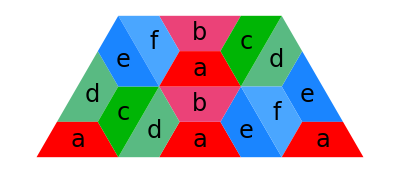

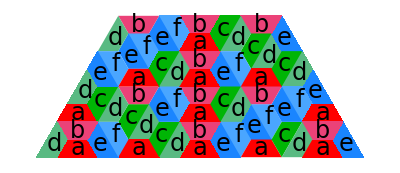

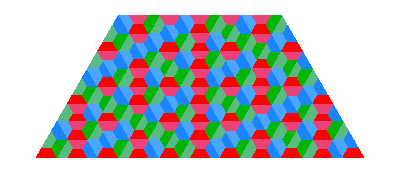

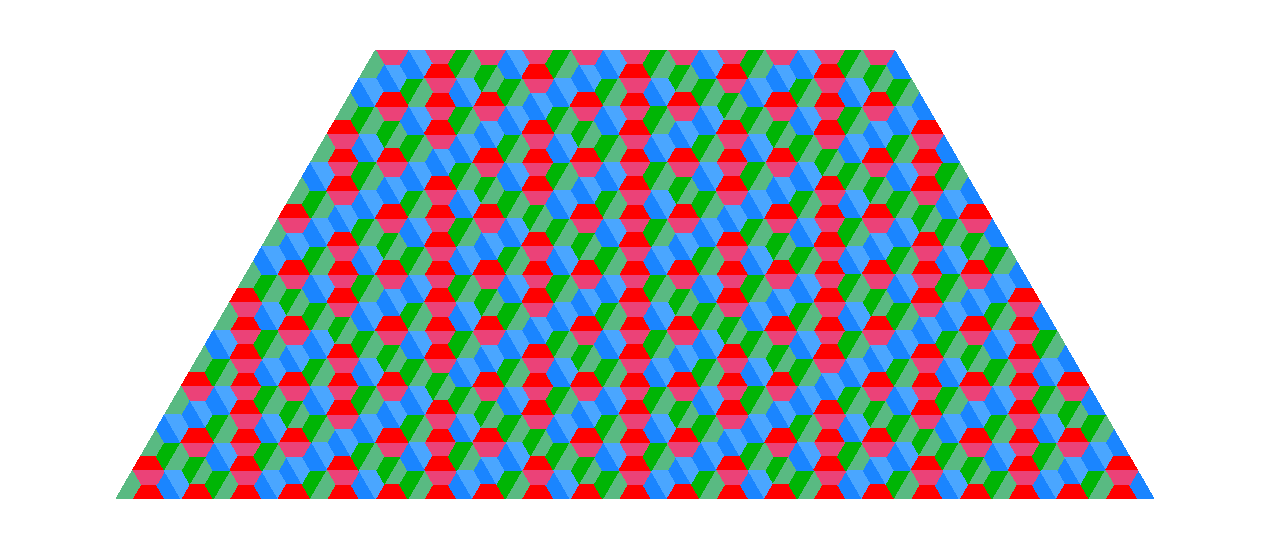

```mathematica
Graphics[polygonsColors[ComputeLocations[N[supertile[1,2]]],Map[#⟦1⟧&,supertile[1,2]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,3]]],Map[#⟦1⟧&,supertile[1,3]]]]
Graphics[polygonsColorsPlain[ComputeLocations[N[supertile[1,4]]],Map[#⟦1⟧&,supertile[1,4]]]]
Graphics[polygonsColorsPlain[ComputeLocations[N[supertile[1,5]]],Map[#⟦1⟧&,supertile[1,5]]]]
```

## 3.Computing Collared Tiles, stableEdges, collaredVertices (run 1,2)

```mathematica
timingList1={};
tiles=Expand[FullSimplify[supertile[1,5]]];
(*tilesLocations={tile1_written_as_list_of_locations, length of tile2_written_as_list_of_locations,...}. *)
AppendTo[timingList1,Timing[tilesLocations=ComputeLocations[tiles];"tilesLocations"]];
tilesLengths=Map[Length,tilesLocations];
(*tilesLocationsAsEdges={tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_of_positive_edges,...}. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
(*tilesEdgesDirections= directions of each tile where 1= same direction, -1=opposite directions. tile has counterclockwise direction. edge has positive direction.*)
(*AppendTo[timingList1,Timing[tilesEdgesDirections=Map[computeEdgesDirections,tilesLocations];"tilesEdgesDirections"]];*)
AppendTo[timingList1,Timing[tilesEdgesDirections=Map[prototilesDirections⟦#⟦1⟧⟧&,tiles];"tilesEdgesDirections"]];

computePositiveEdgesLocations=Function[{index},Module[{edge,lastedge,tileLocations},
tileLocations=tilesLocations⟦index⟧;
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[tilesEdgesDirections⟦index⟧⟦i⟧==1,edge,{edge⟦2⟧,edge⟦1⟧}],{i,1,Length[tileLocations]-1}],If[tilesEdgesDirections⟦index⟧⟦Length[tileLocations]⟧==1,{lastedge},{{lastedge⟦2⟧,lastedge⟦1⟧}}]]]];
AppendTo[timingList1,Timing[tilesLocationsAsEdges=Table[computePositiveEdgesLocations[i],{i,1,Length[tilesLocations]}];"tilesLocationsAsEdges"]];
(*accumulationsOfTilesLengths=Accumulate[{length of tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_positive_edges,... }]*)
accumulationsOfTilesLengths=Accumulate[tilesLengths];
(*tilesLocationsAsEdgesFlattened = list of all edges as pairs of locations (in the supertile)*)
tilesLocationsAsEdgesFlattened=Flatten[tilesLocationsAsEdges,1];
(*commonTilesLocationsAsEdgesIndices gives keysE and edgesToEdgesOfTiles (read below)*)
AppendTo[timingList1,Timing[positionIndexOftilesLocationsAsEdgesFlattened=Normal[PositionIndex[tilesLocationsAsEdgesFlattened]];"positionIndexOftilesLocationsAsEdgesFlattened"]];
(*edgesLocations = unique positive edges (i.e. the location of the positive edge is unique) *)
edgesLocations=Keys[positionIndexOftilesLocationsAsEdgesFlattened];
(*edgesToEdgesOfTiles = {{i1,i2},{i3,i4}...} where the positive edges at i1,i2, in tilesLocationsAsEdgesFlattened are the same.  *)
edgesToEdgesOfTiles=Values[positionIndexOftilesLocationsAsEdgesFlattened];
(*if {i1,i2} has length 2 then the edge at i1,i2 is an interior edge of the supertile. If it has length 1 then it is a bounded edge of the supertile:*)
{bEdges,iEdges}=Values[Sort[Normal[PositionIndex[Map[Length,edgesToEdgesOfTiles]]]]];
(*{bEdges,iEdges}=Values[PositionIndex[Map[Length,edgesToEdgesOfTiles]]];*)
iEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[iEdges]];
bEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[bEdges]];
iEdgesToSingletEdges=Map[#⟦1⟧&,iEdgesToEdgesOfTiles];
iEdgesLocations=tilesLocationsAsEdgesFlattened[[iEdgesToSingletEdges]];
bEdgesLocations=tilesLocationsAsEdgesFlattened[[Flatten[bEdgesToEdgesOfTiles]]];
(*  The tiling T contains the supertile; thus interior edges of the supertile are edges of the tiling T.
 An edge of the tiling T is a pair {(tile,indexOfEdgeInPrototile),(tile,indexOfEdgeInPrototile)}.
 edgeAsPairsOfPrototileNumbers =  {{prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}} Dictionary-sorted.
iEdgesAsPairsOfPrototileNumbers =  { Sort({prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}),...} !!This list has lots of multiplicities! *)
(*an interior edge in the supertile is a pair of edges that have common locations*)
bsearchMaxInaccumulationsOfTilesLengths[elem_]:=Module[{n0=1,n1=Length[accumulationsOfTilesLengths],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[accumulationsOfTilesLengths[[m]]==elem,While[accumulationsOfTilesLengths[[m]]==elem,m--];
Return[m+1]];
If[accumulationsOfTilesLengths[[m]]<elem,n0=m+1,n1=m-1]];
If[accumulationsOfTilesLengths[[m]]>elem,m,m+1]];

Clear[t1,i1,t2,i2]
unflattentedgeflattened=Function[tedgeflattenedNumber,Module[{tileNumber},
tileNumber=bsearchMaxInaccumulationsOfTilesLengths[tedgeflattenedNumber];
{tileNumber,If[tileNumber==1, tedgeflattenedNumber, tedgeflattenedNumber-accumulationsOfTilesLengths⟦tileNumber-1⟧]}]];
iEdgesAsPairsOfTiles=Map[Apply[Sort[{unflattentedgeflattened[#1],unflattentedgeflattened[#2]}]&,#]&,iEdgesToEdgesOfTiles];
iEdgesAsPairsOfPrototileNumbers=Table[{{t1,i1},{t2,i2}}=iEdgesAsPairsOfTiles⟦i⟧;Sort[{{tiles⟦t1⟧⟦1⟧,i1},{tiles⟦t2⟧⟦1⟧,i2}}],{i,1,Length[iEdgesAsPairsOfTiles]}];
Clear[t1,i1,t2,i2]
```

```mathematica
Take[tiles,10]//ColumnForm
tilesLocationsAsEdges//Length
```

{1,{62,0}}
{5,{68,0}}
{2,{66,2 √3}}
{4,{62,2 √3}}
{5,{71,√3}}
{4,{68,4 √3}}
{6,{66,2 √3}}
{1,{68,0}}
{2,{66,4 √3}}
{6,{60,4 √3}}

1024

```mathematica
timingList1//ColumnForm
```

{0.01846,tilesLocations}
{0.00138,tilesEdgesDirections}
{0.03343,tilesLocationsAsEdges}
{0.00528,positionIndexOftilesLocationsAsEdgesFlattened}

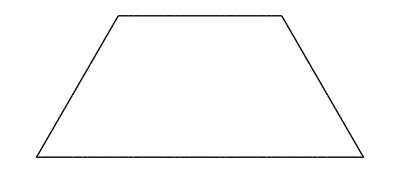

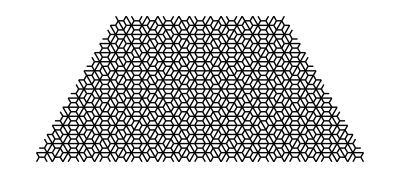

```mathematica
Graphics[Line[bEdgesLocations]]
Graphics[Line[iEdgesLocations]]
```

```mathematica
(*iEdgesAsPairsOfPrototileNumbers[[3]]
tilesLocationsAsEdges[[1]]
tilesLocationsAsEdges[[1]][[3]]
tilesLocationsAsEdges[[3]]
tilesLocationsAsEdges[[3]][[6]]*)
```

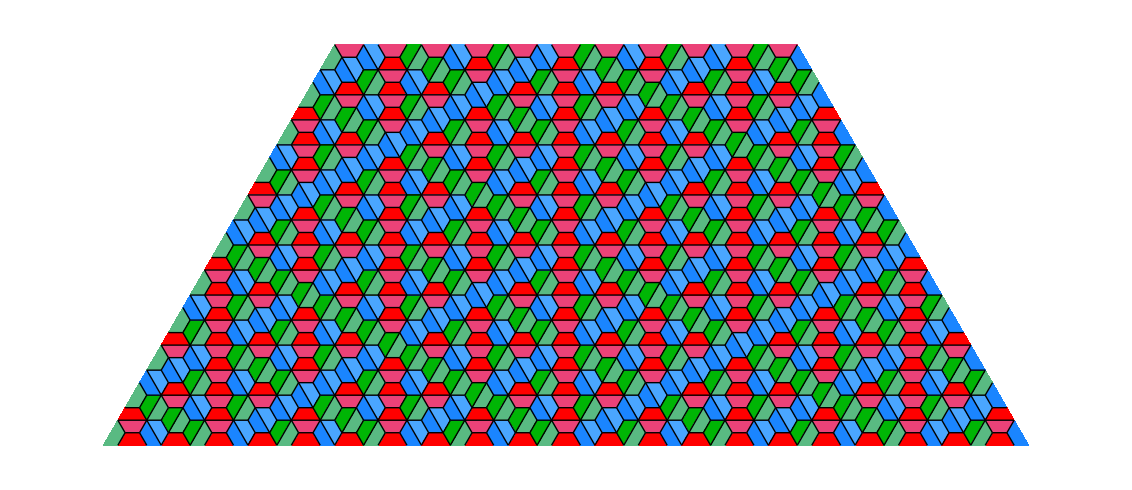

```mathematica
Show[Graphics[polygonsColorsPlain[ComputeLocations[supertile[1,5]],Map[#⟦1⟧&,supertile[1,5]]]],Graphics[Line[iEdgesLocations]]]
```

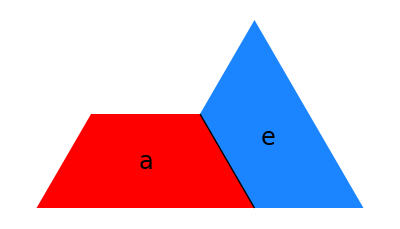

```mathematica
(*drawiEdges=Function[ieNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];*)
drawiEdges=Function[ieNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];
drawiEdges[1]
```

```mathematica
iEdgesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[iEdgesAsPairsOfPrototileNumbers]]];
iEdgesRepresentatives//Length
sEdges=iEdgesAsPairsOfPrototileNumbers⟦iEdgesRepresentatives⟧
drawsEdges=Function[i,drawiEdges[iEdgesRepresentatives⟦i⟧]];
drawWsEdges=Function[seNum,Module[{se,wse},
se=Map[#⟦1⟧&,iEdgesAsPairsOfTiles⟦iEdgesRepresentatives⟦seNum⟧⟧];
wse=Flatten[Map[ωTile[tiles⟦#⟧]&,se],1];
Graphics[Join[polygonsColors[ComputeLocations[wse],Map[#⟦1⟧&,wse]],Map[Line,λ ComputeLocations[tiles⟦se⟧]]]]]];
```

24

{{{1,2},{5,3}},{{1,3},{2,3}},{{1,4},{4,3}},{{5,1},{6,1}},{{2,4},{5,2}},{{1,1},{2,1}},{{2,2},{4,4}},{{3,1},{4,1}},{{4,3},{5,2}},{{5,3},{6,3}},{{1,3},{5,4}},{{4,2},{6,4}},{{1,4},{6,2}},{{1,2},{3,4}},{{2,2},{6,3}},{{2,4},{3,3}},{{3,2},{5,4}},{{1,3},{4,2}},{{3,3},{4,3}},{{4,4},{5,3}},{{3,3},{6,2}},{{2,3},{6,4}},{{2,3},{3,2}},{{3,4},{6,3}}}

24

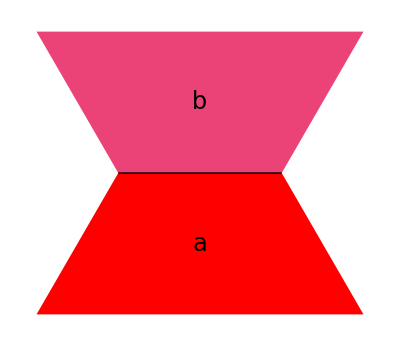
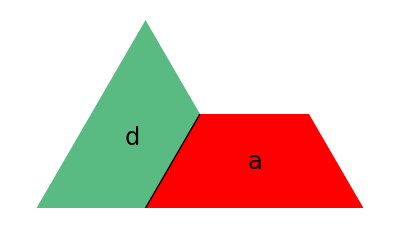
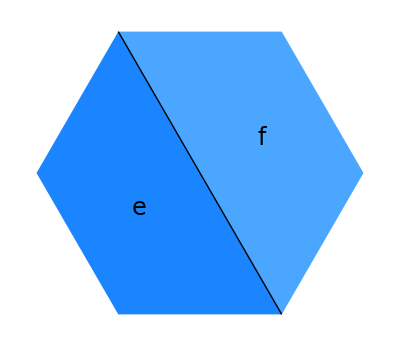
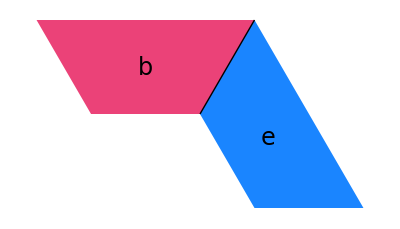
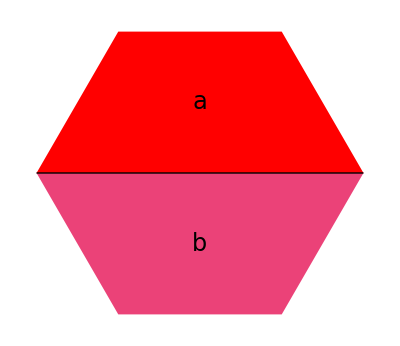
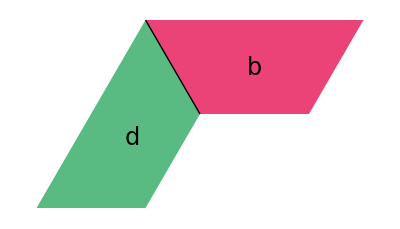
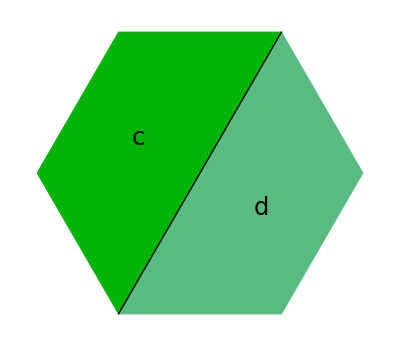
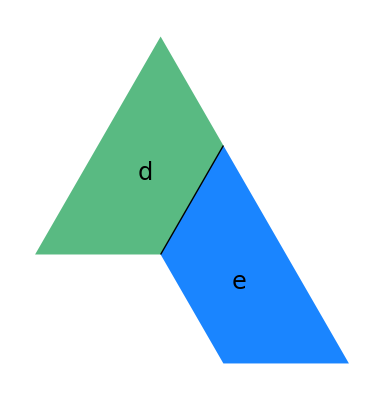
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*sEdges*)
iEdgesRepresentatives//Length
Map[drawiEdges,iEdgesRepresentatives]
```

```mathematica
xxx=Map[drawiEdges,iEdgesRepresentatives];
yyy=Table[Style[StringForm["se_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
Grid[{Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,21,Length[xxx]}]},Frame->All]
```

se_1=
-Graphics- | se_2=
-Graphics- | se_3=
-Graphics- | se_4=
-Graphics- | se_5=
-Graphics-
se_6=
-Graphics- | se_7=
-Graphics- | se_8=
-Graphics- | se_9=
-Graphics- | se_10=
-Graphics-
se_11=
-Graphics- | se_12=
-Graphics- | se_13=
-Graphics- | se_14=
-Graphics- | se_15=
-Graphics-
se_16=
-Graphics- | se_17=
-Graphics- | se_18=
-Graphics- | se_19=
-Graphics- | se_20=
-Graphics-

se_21=
-Graphics- | se_22=
-Graphics- | se_23=
-Graphics- | se_24=
-Graphics-

```mathematica
(*iedgesLocationsAsVertices={positive_edge1, positive_edge2,...}, where these edges are interior edges of the supertile written as positive edges and their location is unique. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
iedgesLocationsAsVertices=iEdgesLocations;
(*iedgesLocationsAsVerticesFlattened = all possible vertices as locations (coming from the interior edges in the supertile)*)
iedgesLocationsAsVerticesFlattened=Flatten[iedgesLocationsAsVertices,1];
(*commonVerticesIndicesInEdgesLocationsAsVertices gives keysV and valuesV (read below)*)
positionIndexOfiedgesLocationsAsVerticesFlattened=PositionIndex[iedgesLocationsAsVerticesFlattened];
(*keysV = unique vertices (their location is unique) *)
verticesLocations=Keys[positionIndexOfiedgesLocationsAsVerticesFlattened];(*representatives of common locations of the vertices*)
(*valuesV = {{i1,i2...},{j3,j4...}...} where the vertices at i1,i2, in iedgesLocationsAsVerticesFlattened are the same. The goal is to obtain the edges with common vertices  *)
verticesToVerticesOfiEdges=Values[positionIndexOfiedgesLocationsAsVerticesFlattened];(* indices of keysV*)
(*if {i1,i2..} has length >1 then the vertex at i1,i2... is an interior vertex of the interior_edges of the supertile. 
If it has length 1 then it is a boundary vertex of the interior_edges of the supertile:*)

{boundaryVertices,interiorVertices}=Values[Sort[Normal[PositionIndex[Map[Length[#]>MAXDegreeOfBoundaryVertices&,verticesToVerticesOfiEdges]]]]];
interiorVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[interiorVertices]];
boundaryVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[boundaryVertices]];
interiorVerticesToSingleVerticesOfiEdges=Map[#⟦1⟧&,interiorVerticesToVerticesOfiEdges];
interiorVerticesLocations=iedgesLocationsAsVerticesFlattened[[interiorVerticesToSingleVerticesOfiEdges]];
boundaryVerticesLocations=iedgesLocationsAsVerticesFlattened[[Flatten[boundaryVerticesToVerticesOfiEdges]]];
tileNumberEdgeVertexTotileNumberVertex=Function[tileNumberEdgeVertex,Module[{tileNumber,edgeNumberOnTile,vertexNumberOnEdge,initialOrFinalVertexOnEdge,edgeDirection,vertexNumberOnTile},
{{tileNumber,edgeNumberOnTile},vertexNumberOnEdge}=tileNumberEdgeVertex;
edgeDirection=tilesEdgesDirections[[tileNumber]][[edgeNumberOnTile]];
vertexNumberOnTile=edgeNumberOnTile;
If[(edgeDirection==1 && vertexNumberOnEdge==2)||(edgeDirection==-1 && vertexNumberOnEdge==1),vertexNumberOnTile=Mod[vertexNumberOnTile+1,tilesLengths[[tileNumber]],1]];
{tileNumber,vertexNumberOnTile}]];

unflatteniEvertexflattened=Function[ievertexflattenedNumber,
{IntegerPart[(ievertexflattenedNumber+1)/2],Mod[ievertexflattenedNumber,2,1]}];
(*verticesAsListOfIndicesOfTiles={ (iEdgesAsPairsOfPrototileNumbers[positive_edge_i_index], 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
interiorVerticesAsiEdges=Table[Sort[Table[unflatteniEvertexflattened[interiorVerticesToVerticesOfiEdges⟦j⟧⟦i⟧],{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

(*protoVerticesAsListOfIndicesOfEdges={ (positive_edge_i_index, 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
verticesAsListOfTilesEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfTiles⟦iEdgeNumber⟧,index},{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

verticesAsListOfTilesVNumbers=Table[Union[Flatten[Table[{{e1,e2},v}=verticesAsListOfTilesEVNumbers[[j]][[i]];
{tileNumberEdgeVertexTotileNumberVertex[{e1,v}],
tileNumberEdgeVertexTotileNumberVertex[{e2,v}]},{i,1,Length[verticesAsListOfTilesEVNumbers[[j]]]}],1]],{j,1,Length[verticesAsListOfTilesEVNumbers]}];

verticesAsListOfPrototileEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfPrototileNumbers⟦iEdgeNumber⟧,index},
{i,1,Length[interiorVerticesAsiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesAsiEdges]}];

verticesAsListOfPrototileVNumbers=Table[Sort[Table[
{tileNumber,index}=verticesAsListOfTilesVNumbers⟦j⟧⟦i⟧;
{tiles⟦tileNumber⟧⟦1⟧,index},
{i,1,Length[verticesAsListOfTilesVNumbers⟦j⟧]}]],{j,1,Length[verticesAsListOfTilesVNumbers]}];
```

```mathematica
verticesAsListOfPrototileVNumbers//Tally//Length
Take[verticesAsListOfPrototileVNumbers//Tally,10]//ColumnForm
```

20

{{{1,3},{2,4},{5,3}},46}
{{{1,4},{2,3},{4,4}},46}
{{{1,2},{2,1},{3,1},{4,2},{5,2},{6,1}},115}
{{{1,1},{2,2},{3,2},{4,1},{5,1},{6,2}},115}
{{{2,3},{4,4},{5,2},{6,1}},40}
{{{1,3},{3,4},{5,1},{6,2}},40}
{{{4,3},{5,3},{6,4}},45}
{{{1,4},{5,4},{6,3}},45}
{{{1,1},{2,2},{4,3},{6,4}},35}
{{{1,2},{2,1},{3,3},{5,4}},35}

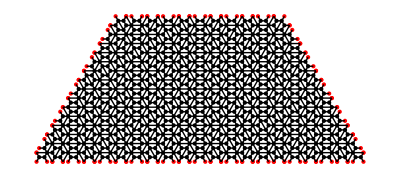

```mathematica
(*boundary vertices should be shown in RED. Interior vertices in Black *)
Show[Graphics[{Red,Point[boundaryVerticesLocations]}],
Graphics[Point[interiorVerticesLocations]],Graphics[Line[iEdgesLocations]]]
```

```mathematica
iEdgesToEdgesOfTiles[[{1,2,5}]]==edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,iEdgesToEdgesOfTiles[[{1,2,5}]]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]]]]
```

True

True

True

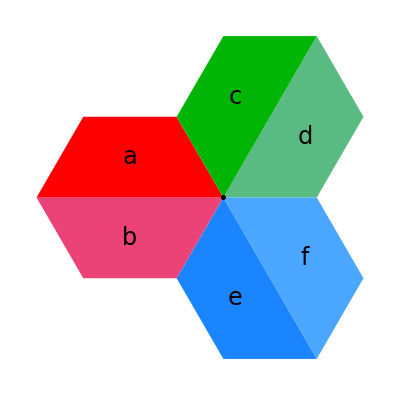

```mathematica
(*drawInteriorVertex=Function[ivNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];*)
drawInteriorVertex=Function[ivNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];
drawInteriorVertex[3]
```

```mathematica
(*drawVertex=Function[index,{drawVertexWithTileLocations[index],drawVertexWithEdges[index]}];
drawVertexWithEdges=Function[index,Line[iedgesLocationsAsVertices⟦Map[#⟦1⟧&,interiorVerticesAsiEdges⟦index⟧]⟧]];
drawVertexWithTileLocations=Function[index,Module[{vertexAsListOfIndicesOfEdges,vertexAsListOfIndicesOfTiles},
vertexAsListOfIndicesOfEdges=Map[#⟦1⟧&,interiorVerticesAsiEdges⟦index⟧];
vertexAsListOfIndicesOfTiles=Union[Flatten[Map[{#⟦1⟧⟦1⟧,#⟦2⟧⟦1⟧}&,iEdgesAsPairsOfTiles⟦vertexAsListOfIndicesOfEdges⟧]]];
PolygonsInColor[tilesLocations⟦vertexAsListOfIndicesOfTiles⟧]]];
PolygonsInColor=Function[polygonCornersList, Table[{color⟦Mod[i,Length[polygonCornersList],1]⟧,Polygon[polygonCornersList⟦i⟧]},{i,1,Length[polygonCornersList]}]];
*)
```

```mathematica
(*drawProtoVertex=Function[protoVertex, Module[{prototileNumber1,prototileNumber2,edgeIndex1,edgeIndex2,vertexIndex,e1,e2,v1,v2},
Table[{{{prototileNumber1,edgeIndex1},{prototileNumber2,edgeIndex2}},vertexIndex}=protoVertex⟦i⟧;
e1=grabEdgeInPolygon[prototiles⟦prototileNumber1⟧,edgeIndex1];
v1=grabVertexInEdgeInPolygon[e1,vertexIndex];
e2=grabEdgeInPolygon[prototiles⟦prototileNumber2⟧,edgeIndex2];
v2=grabVertexInEdgeInPolygon[e2,vertexIndex];

{ {{color⟦Mod[i,Length[color],1]⟧,Polygon[prototiles⟦prototileNumber1⟧]},
{Blue,Line[e1]},{Black,PointSize[.05],Point[v1]}},
{{color⟦Mod[i,Length[color],1]⟧,Polygon[prototiles⟦prototileNumber2⟧]},{Blue,Line[e2]},{Black,PointSize[.05],Point[v2]}}},{i,1,Length[protoVertex]}]
]];

grabEdgeInPolygon=Function[{polygonCorners,edge},{polygonCorners⟦edge⟧,polygonCorners⟦Mod[edge+1,Length[polygonCorners],1]⟧}];
grabVertexInEdgeInPolygon=Function[{edgeAsLocations,initialOrFinalVertex}, If[positiveEdgeQ[edgeAsLocations]==True,edgeAsLocations⟦initialOrFinalVertex⟧,edgeAsLocations⟦Mod[initialOrFinalVertex+1,2,1]⟧]];
Map[Graphics,Flatten[drawProtoVertex[verticesAsListOfPrototileEVNumbers[[1]]],1]]
*)
```

```mathematica
iVerticesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[verticesAsListOfPrototileVNumbers]]];
iVerticesRepresentatives//Length
cVertices=verticesAsListOfPrototileVNumbers⟦iVerticesRepresentatives⟧
drawcVertices=Function[index,drawInteriorVertex[iVerticesRepresentatives⟦index⟧]];
drawWcVertices=Function[cvNum,Module[{cv,wcv},
cv=Map[#⟦1⟧&,verticesAsListOfTilesVNumbers⟦iVerticesRepresentatives⟦cvNum⟧⟧];
wcv=Flatten[Map[ωTile[tiles⟦#⟧]&,cv],1];
Graphics[Join[polygonsColors[ComputeLocations[wcv],Map[#⟦1⟧&,wcv]],Map[Line,λ ComputeLocations[tiles⟦cv⟧]]]]]];
```

20

{{{1,3},{2,4},{5,3}},{{1,4},{2,3},{4,4}},{{1,2},{2,1},{3,1},{4,2},{5,2},{6,1}},{{1,1},{2,2},{3,2},{4,1},{5,1},{6,2}},{{2,3},{4,4},{5,2},{6,1}},{{1,3},{3,4},{5,1},{6,2}},{{4,3},{5,3},{6,4}},{{1,4},{5,4},{6,3}},{{1,1},{2,2},{4,3},{6,4}},{{1,2},{2,1},{3,3},{5,4}},{{1,4},{2,3},{6,3}},{{1,3},{2,4},{3,4}},{{1,4},{3,1},{4,2},{6,3}},{{2,4},{3,2},{4,1},{5,3}},{{1,3},{3,4},{4,3}},{{3,3},{4,4},{5,4}},{{3,3},{5,4},{6,3}},{{2,4},{5,3},{6,4}},{{2,3},{3,3},{4,4}},{{3,4},{4,3},{6,4}}}

20

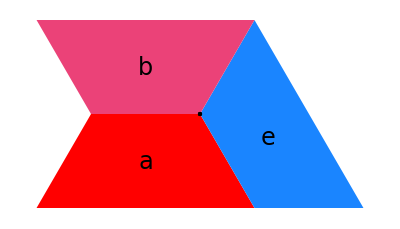
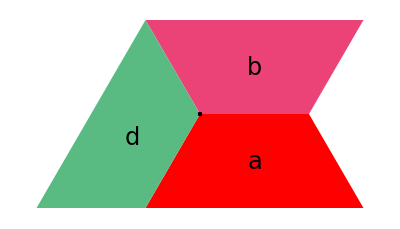
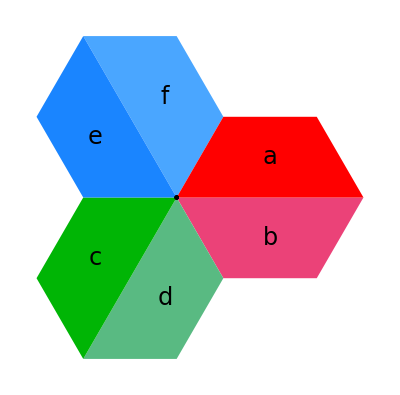
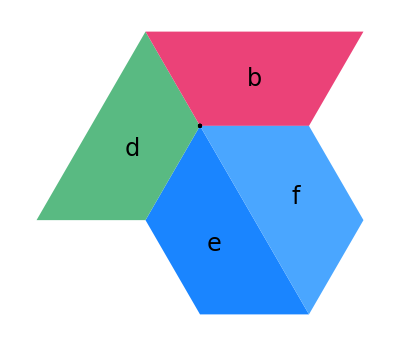
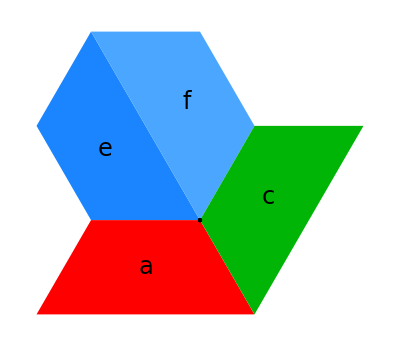
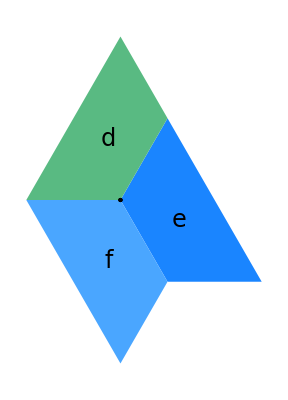
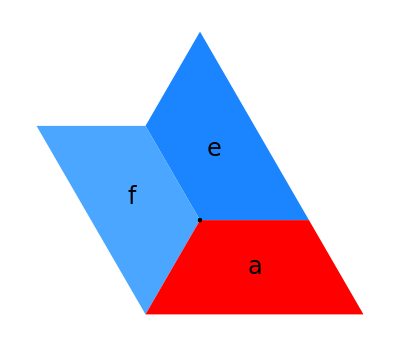
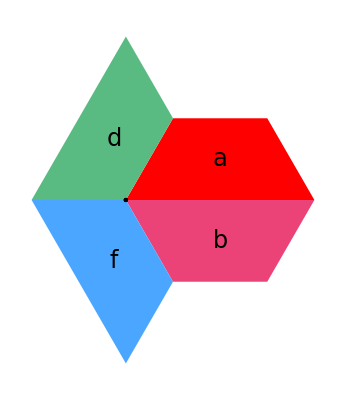
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* protovertices == collared vertices *)
iVerticesRepresentatives//Length
Map[drawInteriorVertex,iVerticesRepresentatives]
```

```mathematica
xxx=Map[drawInteriorVertex,iVerticesRepresentatives];
yyy=Table[Style[StringForm["sv_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
```

sv_1=
-Graphics- | sv_2=
-Graphics- | sv_3=
-Graphics- | sv_4=
-Graphics- | sv_5=
-Graphics-
sv_6=
-Graphics- | sv_7=
-Graphics- | sv_8=
-Graphics- | sv_9=
-Graphics- | sv_10=
-Graphics-
sv_11=
-Graphics- | sv_12=
-Graphics- | sv_13=
-Graphics- | sv_14=
-Graphics- | sv_15=
-Graphics-
sv_16=
-Graphics- | sv_17=
-Graphics- | sv_18=
-Graphics- | sv_19=
-Graphics- | sv_20=
-Graphics-

### results

```mathematica
sEdges
```

{{{1,2},{5,3}},{{1,3},{2,3}},{{1,4},{4,3}},{{5,1},{6,1}},{{2,4},{5,2}},{{1,1},{2,1}},{{2,2},{4,4}},{{3,1},{4,1}},{{4,3},{5,2}},{{5,3},{6,3}},{{1,3},{5,4}},{{4,2},{6,4}},{{1,4},{6,2}},{{1,2},{3,4}},{{2,2},{6,3}},{{2,4},{3,3}},{{3,2},{5,4}},{{1,3},{4,2}},{{3,3},{4,3}},{{4,4},{5,3}},{{3,3},{6,2}},{{2,3},{6,4}},{{2,3},{3,2}},{{3,4},{6,3}}}

```mathematica
cVertices
```

{{{1,3},{2,4},{5,3}},{{1,4},{2,3},{4,4}},{{1,2},{2,1},{3,1},{4,2},{5,2},{6,1}},{{1,1},{2,2},{3,2},{4,1},{5,1},{6,2}},{{2,3},{4,4},{5,2},{6,1}},{{1,3},{3,4},{5,1},{6,2}},{{4,3},{5,3},{6,4}},{{1,4},{5,4},{6,3}},{{1,1},{2,2},{4,3},{6,4}},{{1,2},{2,1},{3,3},{5,4}},{{1,4},{2,3},{6,3}},{{1,3},{2,4},{3,4}},{{1,4},{3,1},{4,2},{6,3}},{{2,4},{3,2},{4,1},{5,3}},{{1,3},{3,4},{4,3}},{{3,3},{4,4},{5,4}},{{3,3},{5,4},{6,3}},{{2,4},{5,3},{6,4}},{{2,3},{3,3},{4,4}},{{3,4},{4,3},{6,4}}}

```mathematica
sEdges//Length
cVertices//Length
```

24

20

## 4. Exponential Matrix, Index Matrix (run 1,2,3)

```mathematica
(*exponential matrix*)
cVerticesAssEdges=verticesAsListOfPrototileEVNumbers[[iVerticesRepresentatives]];
sEdgescVerticesMatrix=ConstantArray[0,{Length[sEdges],Length[cVertices]}];

sEdgescVerticesMatrixIndicesFunction=
Function[cvNumber,Module[{cv,se,vInitialOrFinal,seNumber,value},
cv=cVerticesAssEdges⟦cvNumber⟧;
Table[{se,vInitialOrFinal}=cv⟦i⟧;
seNumber=Position[sEdges,se]⟦1⟧⟦1⟧;
value=If[vInitialOrFinal==1,-1,1];
sEdgescVerticesMatrix⟦seNumber⟧⟦cvNumber⟧+=value;
{{seNumber,cvNumber},value},{i,1,Length[cv]}]]];


sEdgescVerticesMatrixIndices=Table[sEdgescVerticesMatrixIndicesFunction[i],{i,1,Length[cVertices]}];
(*stableEdges-collardVertices Matrix (se1=-cv1+cv9+cv14...*)
Print["δ^0=",sEdgescVerticesMatrix//MatrixForm]
```

δ^0=(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
(*Index Matrix*)
prototilessEdgesMatrix=ConstantArray[0,{Length[prototiles],Length[sEdges]}];
Table[{{p1,e1},{p2,e2}}=sEdges⟦sedgeNumber⟧;
prototilessEdgesMatrix⟦p1⟧⟦sedgeNumber⟧+=prototilesDirections⟦p1⟧⟦e1⟧;
prototilessEdgesMatrix⟦p2⟧⟦sedgeNumber⟧+=prototilesDirections⟦p2⟧⟦e2⟧;,
{sedgeNumber,1,Length[sEdges]}];
Print["δ^1=",prototilessEdgesMatrix//MatrixForm]
```

δ^1=(-1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 1
0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1)

```mathematica
prototilessEdgesMatrix.sEdgescVerticesMatrix//Max
prototilessEdgesMatrix.sEdgescVerticesMatrix//Min
```

0

0

## 5. Homotopy matrices Wv, We, Wf

```mathematica
(*Homotopy ω(prototile) --> prototile : Hverticesp1t1 is the image of the map on the vertices from ω(prototile) to same protitile 1.*)
Hverticesp1t1={1,2,3,4};
Hverticesp1t2={2,3,3,2};
Hverticesp1t3={3,4,4,3};
Hverticesp1t4={4,1,1,4};

Hverticesp1={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp2={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp3={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp4={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp5={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hverticesp6={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4}};
Hvertices={Hverticesp1,Hverticesp2,Hverticesp3,Hverticesp4,Hverticesp5,Hverticesp6}
```

{{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}},{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}},{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}},{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}},{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}},{1,{{1,2,3,4},{2,3,3,2},{3,4,4,3},{4,1,1,4}}}}

```mathematica
wPrototileNumbers=Table[Map[#⟦1⟧&,wPrototile⟦i⟧],{i,1,Length[wPrototile]}]

drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
{t,imageVertices}=Hvertices⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopycVertices=Function[cVertexNum,Module[{cv},
cv=cVertices⟦cVertexNum⟧;
Graphics[Map[drawHomotopyVerticesOfTilesNoGraphics,Table[{cv⟦i,1⟧,Expand[FullSimplify[prototiles⟦cv⟦i,1⟧,1⟧-prototiles⟦cv⟦i,1⟧,cv⟦i,2⟧⟧]]},{i,1,Length[cv]}]]]]];

drawHomotopyVerticesOfTiles=Function[tile,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
{t,imageVertices}=Hvertices⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]]];

drawHomotopyVertices=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

```mathematica
drawHomotopyVerticesPlain=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
{t,imageVertices}=Hvertices⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[{Thickness[.008],Arrowheads[0.05],Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]]},{i,1,Length[imageVertices]}];
Graphics[{polygonsColorsPlain[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];
drawHomotopyVerticesPlain[6]
```

-Graphics-

```mathematica
Table[drawHomotopyVerticesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[drawHomotopyVertices[i],{i,1,Length[prototiles]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[1]
```

-Graphics-

```mathematica
Table[drawHomotopycVertices[i],{i,1,Length[cVertices]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
homotopycVertices=ConstantArray[0,Length[cVertices]];

Clear[cv,ps,vs,locsH,xx,yy,ts,cvNum]
For[cvNum=1,cvNum≤ Length[cVertices],cvNum++,
cv=cVertices⟦cvNum⟧;
cvHpreimage=Table[Position[Hvertices⟦cv⟦i,1⟧,2⟧,cv⟦i,2⟧],{i,1,Length[cv]}];
{ps,vs}=Transpose[cv];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototiles⟦ps⟦i⟧⟧⟦vs⟦i⟧⟧},{i,1,Length[ps]}];
(*Map[ωTile,ts]*)
locsH=Table[ComputeLocations[ωTile[ts⟦i⟧]],{i,1,Length[ts]}];
cvHpreimageLocations=Table[Table[locsH⟦j⟧⟦cvHpreimage⟦j⟧⟦i,1⟧,cvHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[cvHpreimage⟦j⟧]}],{j,1,Length[cvHpreimage]}];
(*cvHpreimage//ColumnForm*)
(*cvHpreimageLocations//Point//Graphics*)
(*Flatten[cvHpreimageLocations,1]*)
cvHpreimageFlattened=Flatten[cvHpreimage,1];
(*cvHpreimageFlattenedTiles=Flatten[Table[ConstantArray[i,Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1]*)
cvHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1];
hcverticesindices=Values[Normal[PositionIndex[Flatten[cvHpreimageLocations,1]]]];

(*hcverticesAsTiles=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedTiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[Flatten[{yy⟦i⟧,xx⟦i⟧}],{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}]
Table[Map[locsH⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧&,hcverticesAsTiles⟦i⟧],{i,1,Length[hcverticesAsTiles]}]*)

hcvertices=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedPrototiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}];
homotopycVertices⟦cvNum⟧=Table[Position[cVertices,hcvertices⟦i⟧]⟦1,1⟧,{i,1,Length[hcvertices]}]]
homotopycVertices
```

{{1,3,12,7},{2,4,11,16},{10,4,13,5},{9,3,14,6},{11,4,16,5},{1,3,20,6},{15,3,7,18},{2,4,8,17},{9,3,15,18},{10,4,19,8},{2,4,11,17},{1,3,12,20},{2,4,13,17},{12,3,14,7},{1,3,20,15},{19,4,16,8},{19,4,8,17},{12,3,7,18},{11,4,19,16},{20,3,15,18}}

```mathematica
cverticesHMtx=ConstantArray[0,{Length[cVertices],Length[cVertices]}];
Table[Table[cverticesHMtx⟦homotopycVertices⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopycVertices⟦i⟧]}],{i,1,Length[homotopycVertices]}];
Print["W_V=",cverticesHMtx//MatrixForm]
```

W_V=(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)

```mathematica
drawHomotopycVertices[1]
Map[drawcVertices,{1,3,12,7}]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[2]
Map[drawcVertices,{2,4,11,16}]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Hedgesp1t1={1,2,3,4};
Hedgesp1t2={2,0,2,0};
Hedgesp1t3={3,0,3,0};
Hedgesp1t4={4,0,4,0};

Hedgesp1={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp2={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp3={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp4={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp5={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedgesp6={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4}};
Hedges={Hedgesp1,Hedgesp2,Hedgesp3,Hedgesp4,Hedgesp5,Hedgesp6}
```

{{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}},{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}},{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}},{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}},{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}},{1,{{1,2,3,4},{2,0,2,0},{3,0,3,0},{4,0,4,0}}}}

```mathematica
prototilesMidEdges=Table[Table[Expand[FullSimplify[(prototiles⟦i⟧⟦j⟧+prototiles⟦i⟧⟦Mod[j+1,Length[prototiles⟦i⟧],1]⟧)/2]],{j,1,Length[prototiles⟦i⟧]}],{i,1,Length[prototiles]}];
ComputeLocationsMidEdges=Function[{tiles},Module[{prototileNumber,translation},Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototilesMidEdges⟦prototileNumber⟧⟦j⟧+translation,{j,1,Length[prototilesMidEdges⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];


drawHomotopyEdgesOfTilesNoGraphics=Function[tile,Module[{locs,t,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[ωTile[tile]];
{t,imageEdges}=Hedges⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{tile}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopysEdges=Function[sEdgeNum,Module[{se},
se=sEdges⟦sEdgeNum⟧;
Graphics[Map[drawHomotopyEdgesOfTilesNoGraphics,Table[{se⟦i,1⟧,Expand[FullSimplify[prototiles⟦se⟦i,1⟧,1⟧-prototilesMidEdges⟦se⟦i,1⟧,se⟦i,2⟧⟧]]},{i,1,Length[se]}]]]]];

drawHomotopyEdgesOfTiles=Function[tile,Graphics[drawHomotopyEdgesOfTilesNoGraphics[tile]]];

drawHomotopyEdges=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
{t,imageEdges}=Hedges⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyEdgesAll=Function[prototilenumber,Module[{locs,t,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
{t,imageEdges}=Hedges⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

```mathematica
drawHomotopyEdgesOfTiles[{1,{0,0}}]
```

-Graphics-

```mathematica
Table[drawHomotopyEdgesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[drawHomotopysEdges[i],{i,1,Length[sEdges]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawsEdges[1]
```

-Graphics-

```mathematica
homotopysEdges=ConstantArray[0,Length[sEdges]];

Clear[se,ps,es,locsH,xx,yy,ts,seNum]
For[seNum=1,seNum≤ Length[sEdges],seNum++,
se=sEdges⟦seNum⟧;
seHpreimage=Table[Position[Hedges⟦se⟦i,1⟧,2⟧,se⟦i,2⟧],{i,1,Length[se]}];
{ps,es}=Transpose[se];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototilesMidEdges⟦ps⟦i⟧⟧⟦es⟦i⟧⟧},{i,1,Length[ps]}];
locsH=Table[Expand[FullSimplify[ComputeLocationsMidEdges[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
seHpreimageLocations=Table[Table[locsH⟦j⟧⟦seHpreimage⟦j⟧⟦i,1⟧,seHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[seHpreimage⟦j⟧]}],{j,1,Length[seHpreimage]}];
seHpreimageFlattened=Flatten[seHpreimage,1];
seHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[seHpreimage⟦i⟧]],{i,1,Length[seHpreimage]}],1];
hsedgesindices=Values[Normal[PositionIndex[Flatten[seHpreimageLocations,1]]]];
hsedges=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hsedgesindices]}];
homotopysEdges⟦seNum⟧=Table[Position[sEdges,hsedges⟦i⟧]⟦1,1⟧,{i,1,Length[hsedges]}];

]
homotopysEdges
```

{{1,4,10},{2,6,2},{3,8,19},{4},{16,8,9},{6},{15,4,20},{8},{19,8,9},{10,4,10},{2,6,11},{18,6,22},{3,8,21},{1,4,24},{15,4,10},{16,8,19},{23,6,11},{2,6,18},{19,8,19},{20,4,10},{19,8,21},{2,6,22},{2,6,23},{24,4,10}}

```mathematica
sedgesHMtx=ConstantArray[0,{Length[sEdges],Length[sEdges]}];
Table[Table[sedgesHMtx⟦homotopysEdges⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopysEdges⟦i⟧]}],{i,1,Length[homotopysEdges]}];
Print["W_E=",sedgesHMtx//MatrixForm]
```

W_E=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Hprototiles={1,2,3,4,5,6};
tilesHMtx=ConstantArray[0,{Length[prototiles],Length[prototiles]}];
Table[tilesHMtx⟦Hprototiles⟦i⟧⟧⟦i⟧+=1,{i,1,Length[Hprototiles]}];
Print["W_F=",tilesHMtx//MatrixForm]
```

W_F=(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
δ0=sEdgescVerticesMatrix
δ1=prototilessEdgesMatrix
Wv=cverticesHMtx
We=sedgesHMtx
Wf=tilesHMtx
```

{{-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{1,-1,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0},{0,0,1,-1,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,-1,1,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,1,-1,0,0},{0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,-1,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,-1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0,-1,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,1,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1}}

{{-1,-1,-1,0,0,1,0,0,0,0,-1,0,-1,-1,0,0,0,-1,0,0,0,0,0,0},{0,1,0,0,1,-1,1,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,-1,-1,0,-1,0,-1,0,-1,1},{0,0,1,0,0,0,-1,-1,1,0,0,1,0,0,0,0,0,1,1,-1,0,0,0,0},{1,0,0,-1,-1,0,0,0,-1,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0},{0,0,0,1,0,0,0,0,0,-1,0,-1,1,0,-1,0,0,0,0,0,1,-1,0,-1}}

{{1,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0},{0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0,0,1,0,1},{0,1,1,0,1,0,0,1,0,1,1,0,1,0,0,1,1,0,1,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,0,0,0},{0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,1},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,0,0,0,1}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,2,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,1,1,0,0,0,1,0,0,1,0,0,1,0,1,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,2,0,0,0,0,1,0,0,0,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,2,0,1,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1}}

{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
δ1.δ0
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
We.δ0//MatrixForm
δ0.Wv//MatrixForm
```

(-1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | -2 | 2 | -1 | 1 | 1 | 0 | 0 | 1 | -1 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | -1
-1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | -1 | 1 | 1 | 0 | 1 | -1 | 0 | 1 | 2 | -2 | 0 | -1
0 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | -2 | 2 | 1 | 0 | 2 | -2
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | -2 | 2 | -1 | 1 | 1 | 0 | 0 | 1 | -1 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 0 | 0 | -1 | 1 | 1 | -1 | 1 | -1
-1 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | -1 | 1 | 1 | 0 | 1 | -1 | 0 | 1 | 2 | -2 | 0 | -1
0 | 0 | 0 | 1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | -1 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | -2 | 2 | 1 | 0 | 2 | -2
0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1)

```mathematica
We.δ0==δ0.Wv
```

True

```mathematica
Wf.δ1//MatrixForm
δ1.We//MatrixForm
Wf.δ1==δ1.We
```

(-1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 1
0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1)

(-1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 1
0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1)

True